```mathematica
𝓊P[c_] := c^-ρ;
𝓊[c_] := (c^(1-ρ))/(1-ρ);
𝓋P[x_] :=  (x^-ρ);
𝓋[x_] :=  (x^(1-ρ))/(1-ρ);
ρ = 6;ω = 1;η = .15;ybar = ω;cmin = .8; cmax = 1.2;
cstar = c /. FindRoot[𝓊P[c] == .5 𝓋P[ω+ybar+η-c]+.5 𝓋P[ω+ybar-η-c],{c,.5,1.5}];
```

```mathematica
α =.75;𝒸Bar = 3;Euc = .5 𝓊[𝒸Bar-α]+.5 𝓊[𝒸Bar+α];E𝓊Pc = .5 𝓊P[𝒸Bar-α]+.5 𝓊P[𝒸Bar+α];
πStar = (πStar /. FindRoot[𝓊[𝒸Bar-πStar] == Euc,{πStar,0,.1}]);
μStar = (μStar /. FindRoot[𝓊P[𝒸Bar-μStar] == E𝓊Pc,{μStar,0,.1}]);
```

```mathematica
μStar
```

0.493582

```mathematica
πStar
```

0.453849

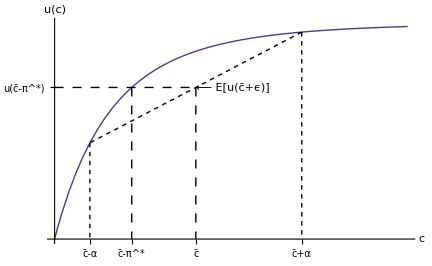

```mathematica
RiskAndPSPremiaRisk = Show[
Plot[
𝓊[c],{c,2,4.5}
,ImageSize->{72. 6.,72. 6. /GoldenRatio}
,Ticks->{{{𝒸Bar-α,"c̄-α"},{𝒸Bar-πStar,"c̄-π^*"},{𝒸Bar,"c̄"},{𝒸Bar+α,"c̄+α"}},{{Euc,"u(c̄-π^*)"}}}
,AxesOrigin->{2,𝓊[2]}
,AxesLabel->{c,"u(c)"}
,BaseStyle->{FontSize->14}
,PlotStyle->Thick
]
,Graphics[{Thick,Dashing[{.015}],Line[{{2,Euc},{𝒸Bar,Euc}}]}]
,Graphics[{Thick,Dashing[{.0075}],Line[{{𝒸Bar+α,𝓊[𝒸Bar+α]},{𝒸Bar-α,𝓊[𝒸Bar-α]}}]}]
,Graphics[{Thick,Dashing[{.015}],Line[{{𝒸Bar-πStar,Euc},{𝒸Bar-πStar,𝓊[2]}}]}]
,Graphics[{Thick,Dashing[{.0075}],Line[{{𝒸Bar-α,𝓊[𝒸Bar-α]},{𝒸Bar-α,𝓊[2]}}]}]
,Graphics[{Thick,Dashing[{.0075}],Line[{{𝒸Bar+α,𝓊[𝒸Bar+α]},{𝒸Bar+α,𝓊[2]}}]}]
,Graphics[{Thick,Dashing[{.015}],Line[{{𝒸Bar,Euc},{𝒸Bar,𝓊[2]}}]}]
,Graphics[Text[" ⟵ E[u(c̄+ϵ)]",{𝒸Bar,Euc},{-1,0}]]
]
```

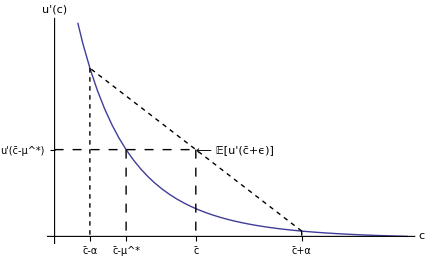

```mathematica
RiskAndPSPremiaPrec = Show[
Plot[
𝓊P[c],{c,2,4.5}
,ImageSize->{72. 6.,72. 6. /GoldenRatio}
,Ticks->{{{𝒸Bar-α,"c̄-α"},{𝒸Bar-μStar,"c̄-μ^*"},{𝒸Bar,"c̄"},{𝒸Bar+α,"c̄+α"}},{{E𝓊Pc,"u'(c̄-μ^*)"}}}
,AxesOrigin->{2,𝓊P[4.5]}
,AxesLabel->{c,"u'(c)"}
,BaseStyle->{FontSize->14}
,PlotStyle->Thick
]
,Graphics[{Thick,Dashing[{.015}],Line[{{2,E𝓊Pc},{𝒸Bar,E𝓊Pc}}]}]
,Graphics[{Thick,Dashing[{.0075}],Line[{{𝒸Bar+α,𝓊P[𝒸Bar+α]},{𝒸Bar-α,𝓊P[𝒸Bar-α]}}]}]
,Graphics[{Thick,Dashing[{.015}],Line[{{𝒸Bar-μStar,E𝓊Pc},{𝒸Bar-μStar,𝓊P[4.5]}}]}]
,Graphics[{Thick,Dashing[{.0075}],Line[{{𝒸Bar-α,𝓊P[𝒸Bar-α]},{𝒸Bar-α,𝓊P[4.5]}}]}]
,Graphics[{Thick,Dashing[{.0075}],Line[{{𝒸Bar+α,𝓊P[𝒸Bar+α]},{𝒸Bar+α,𝓊P[4.5]}}]}]
,Graphics[{Thick,Dashing[{.015}],Line[{{𝒸Bar,E𝓊Pc},{𝒸Bar,𝓊P[4.5]}}]}]
,Graphics[Text[" ⟵ 𝔼[u'(c̄+ϵ)]",{𝒸Bar,E𝓊Pc},{-1,0}]]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/Data/Courses/Choice/LectureNotes/Consumption/Handouts/RiskAndPSPremia/Software/Mathematica

```mathematica
Export["../../Figures/RiskAndPSPremiaRisk.pdf",RiskAndPSPremiaRisk];
Export["../../Figures/RiskAndPSPremiaRisk.eps",RiskAndPSPremiaRisk];
Export["../../Figures/RiskAndPSPremiaRisk.jpg",RiskAndPSPremiaRisk,ImageSize->72 9];
```

```mathematica
Export["../../Figures/RiskAndPSPremiaPrec.eps",RiskAndPSPremiaPrec];
Export["../../Figures/RiskAndPSPremiaPrec.pdf",RiskAndPSPremiaPrec];
Export["../../Figures/RiskAndPSPremiaPrec.jpg",RiskAndPSPremiaPrec,ImageSize->72 9];
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

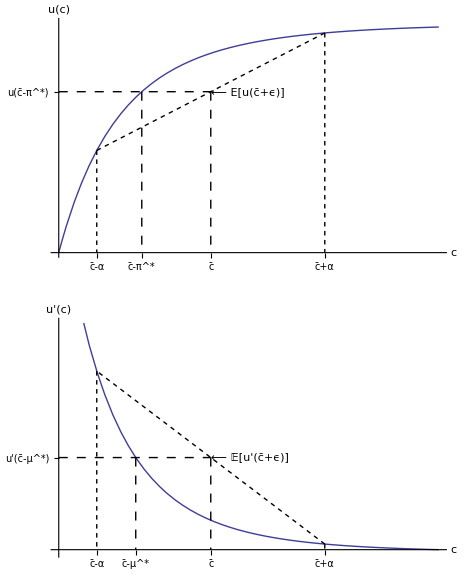

```mathematica
RiskAndPSPremiaFigs=Show[GraphicsArray[{{RiskAndPSPremiaRisk},{RiskAndPSPremiaPrec}}]]
```

```mathematica
Export["../../Figures/RiskAndPSPremiaFigs.eps",RiskAndPSPremiaFigs];
Export["../../Figures/RiskAndPSPremiaFigs.pdf",RiskAndPSPremiaFigs];
Export["../../Figures/RiskAndPSPremiaFigs.jpg",RiskAndPSPremiaFigs,ImageSize->72 9];
```